## Уравнения

```mathematica
(* заведем точки в терминах {μ, ν} игнорируя точку {0, 1} *)
dots = {{-2,0},{-1,-1},{0,0},{1,-1}};
(*dots = {{-1, 0},{-2 ,0}, {1, 0}, {0,0}};*)
```

```mathematica
(* научимся красиво печатать наши уравнения *)
ClearAll[σ,α, PrePrint];
PrePrint[obj_] := obj/. {α[{x_, y_}]-> Subscript[α, x,y]};
```

```mathematica
(* заведем переменные *)
vars = Map[α, dots];
(* пронумеруем для удобства переменные *)
Table[{i, vars[[i]]}, {i, 1, 4}]ᵀ // PrePrint // TableForm
```

1 | 2 | 3 | 4
α_(-2,0) | α_(-1,-1) | α_(0,0) | α_(1,-1)

Далее будем считать: vars⟦2⟧ -- x, vars⟦4⟧ -- y.

```mathematica
(* научимся составлять уравнение для аппрокисмации nного порядка *)
ClearAll[GetEq];
GetEq[k_] :=  (Total@Map[α[#]&,dots ] == 1) /; k == 0;
GetEq[k_] :=  (Total@Map[(#[[1]]-σ #[[2]])^k α[#]&,dots ] == (-σ)^k) /; k > 0;
```

```mathematica
(*Subscript[Σ, μ, ν](μ - σ ν)^k Subscript[α^ν, μ] = (-σ)^k*)
```

```mathematica
(* первый порядок аппроксимации *)
eqs1 = {GetEq[0], GetEq[1]};
sol1 = FullSimplify@Solve[eqs1, {vars[[4]], vars[[2]]}];
sol1ᵀ //PrePrint // TableForm
```

α_(1,-1)→1/2 (1-2 σ+(1+σ) α_(-2,0)+(-1+σ) α_(0,0))
α_(-1,-1)→1/2 (1+2 σ-(3+σ) α_(-2,0)-(1+σ) α_(0,0))

```mathematica
GetEq[2]
```

```mathematica
eq = 4 α[{-2,0}]+(-1+σ)^2 α[{-1,-1}]+(1+σ)^2 α[{1,-1}]-σ^2;
```

```mathematica
(* второй порядок аппроксимации *)
eqs2 = {GetEq[0], GetEq[1], GetEq[2]} ;
sol2 = Solve[eqs2, {vars[[4]], vars[[3]], vars[[2]]}];
sol2ᵀ//PrePrint // TableForm
```

α_(1,-1)→-(σ-2 σ^2+2 α_(-2,0)+2 σ α_(-2,0))/(2 (1+σ))
α_(0,0)→-(1-4 σ^2+3 α_(-2,0)+4 σ α_(-2,0)+σ^2 α_(-2,0))/((-1+σ) (1+σ))
α_(-1,-1)→-(σ+2 σ^2-6 α_(-2,0)-2 σ α_(-2,0))/(2 (-1+σ))

```mathematica
(* немного пошаманим, чтобы получить уравнение прямой *)
ans = (sol2[[1, 1]][[2]] /.Solve[sol2[[1, 3]][[1]] == sol2[[1, 3]][[2]], vars[[1]]]);
ans = FullSimplify[ans[[1]]];
vars[[4]] == ans // PrePrint
```

α_(1,-1)==((-2+σ) σ-(-1+σ^2) α_(-1,-1))/((1+σ) (3+σ))

```mathematica
(* третий порядок аппроксимации *)
eqs3 = {GetEq[0], GetEq[1], GetEq[2], GetEq[3]} ;
sol3 = Solve[eqs3, vars];
sol3ᵀ//PrePrint // TableForm
```

α_(-2,0)→-(σ-4 σ^3)/(2 (3+4 σ+σ^2))
α_(-1,-1)→-(2 σ+3 σ^2-2 σ^3)/(2 (-1+σ) (1+σ))
α_(0,0)→-(2-σ-8 σ^2+4 σ^3)/(2 (-1+σ) (1+σ))
α_(1,-1)→-(2 σ-5 σ^2+2 σ^3)/(2 (1+σ) (3+σ))

## Визуализация

```mathematica
par = 0; (* ноль для монотонных по Фридрихсу *)
square = ImplicitRegion[par < vars[[1]]<1 && par < vars[[3]]<1,{vars[[1]],vars[[3]]}];
```

```mathematica
(* вставить эти уравнения в MapReg *)
{sol1[[1]][[2]][[2]] /. {vars[[3]] -> v3, vars[[1]] -> v1},
sol1[[1]][[1]][[2]]/. {vars[[3]] -> v3, vars[[1]] -> v1}}
```

{1/2 (1+2 σ-v3 (1+σ)-v1 (3+σ)),1/2 (1+v3 (-1+σ)-2 σ+v1 (1+σ))}

```mathematica
ClearAll[MapReg];
MapReg[{v3_,v1_}, σ_]:={1/2 (1+2 σ-v3 (1+σ)-v1 (3+σ)),1/2 (1+v3 (-1+σ)-2 σ+v1 (1+σ))};
```

```mathematica
(* Вывдем вершины параллелограмма *)
σ0 = 1/2;
{{x, y}, MapReg[{1,1},σ0], MapReg[{1,0},σ0], MapReg[{0,1},σ0], MapReg[{0,0},σ0]}ᵀ // TableForm
```

x | -3/2 | 1/4 | -3/4 | 1
y | 1/2 | -1/4 | 3/4 | 0

```mathematica
(* найдём B2 *)
Solve[D[({x, a x + b} - {x1, y1}).({x, a x + b} - {x1, y1}), x] == 0, x]
```

{{x→(-a b+x1+a y1)/(1+a^2)}}

```mathematica
GetB2[{x1_, y1_}] := Module[{a, b, x0}, 
{a, b} = CoefficientList[GetLine[x, σ], x];
x0 = (-a b+x1+a y1)/(1+a^2);
{x0, a x0 + b}];
```

```mathematica
FullSimplify@GetB2[MapReg[{1,1},σ]]
```

{(-27+σ (16+σ (-3+2 σ)))/(2 (9+σ (-6+σ (5+4 (-2+σ) σ)))),((-1+σ) (-3+σ (-8+σ+2 σ^2)))/(9+σ (-6+σ (5+4 (-2+σ) σ)))}

```mathematica
(* вставить эти уравнения в GetLine *)
ans /. {vars[[2]] -> x}
```

((-2+σ) σ-x (-1+σ^2))/((1+σ) (3+σ))

```mathematica
Solve[D[({x, a x + b} - {x1, y1}).({x, a x + b} - {x1, y1}), x] == 0, x]
```

```mathematica
ClearAll[GetLine];
GetLine[x_, σ_]:=((-2+σ) σ-x (-1+σ^2))/((1+σ) (3+σ));
```

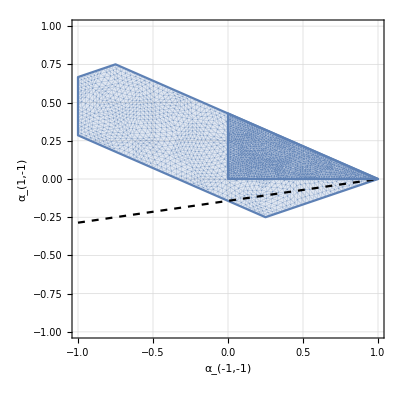

```mathematica
(*Manipulate[*)
σ0 = 0.5;
P = TransformedRegion[square, MapReg[{#1, #2}, σ0]&];
Show[{
RegionPlot[P, Axes->True, PlotRange->{{-1, 1}, {-1, 1}}, AxesLabel->({vars[[2]], vars[[4]]}// PrePrint), GridLines->Automatic, PlotStyle->Opacity[0.2]],
RegionPlot[P, Axes->True, PlotRange->{{0, 1}, {0, 1}}],
Plot[GetLine[x, σ0], {x, -1, 1}, PlotStyle->{Black, Dashed}]
}]
(*, {{σ0, 0.5}, 0, 1}]*)
```